# Harmonický ustálený stav (HUS), přenos, časová oblast, stejnosměrný stav

-Graphics-
Vstupní napětí  uZ[t]má sinusový průběh o frekvenci f=100 Hz.Fázor vstupního napětí má hodnotu Û=3+6j. Hodnoty součástek jsou následující:
R1=10 kΩ,
R2=10 kΩ,
R3=10 kΩ,
C2=10 nF,
L1=10 mH.
Řešte obvod v HUS. Zobrazte napětí uout[t] v časovém intervalu 0≤t≤0.3. Vykreslete přenos obvodu pro 10≤ω≤10^7.

### PODROBNÉ řešení příkladu v HUSu + určení přenosu obvodu

-Graphics-

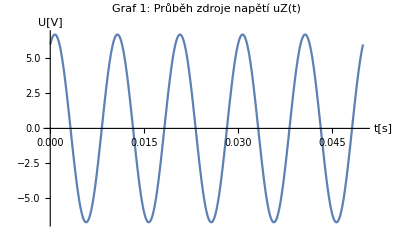

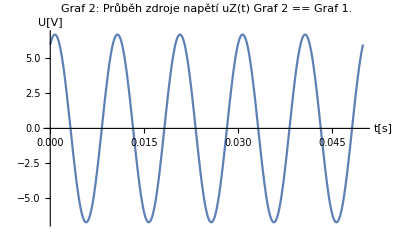

{{iuZ→((3/5000+(3 ⅈ)/2500) (-5000 ⅈ+ω) (-1000000 ⅈ+ω))/(-10000000000-1020000 ⅈ ω+3 ω^2),iR1→((3/5000+(3 ⅈ)/2500) (-5000 ⅈ ω+ω^2))/(-10000000000-1020000 ⅈ ω+3 ω^2),iR2→((3/10000+(3 ⅈ)/5000) ω (-1000000 ⅈ+ω))/(-10000000000-1020000 ⅈ ω+3 ω^2),iR3→((3/10000+(3 ⅈ)/5000) (-10000000000-1010000 ⅈ ω+ω^2))/(-10000000000-1020000 ⅈ ω+3 ω^2),iC2→((3/10000+(3 ⅈ)/5000) ω (-1000000 ⅈ+ω))/(-10000000000-1020000 ⅈ ω+3 ω^2),iL1→((1200-600 ⅈ) (-5000 ⅈ+ω))/(-10000000000-1020000 ⅈ ω+3 ω^2),u1→3+6 ⅈ,u2→((3+6 ⅈ) (-10000000000-1010000 ⅈ ω+ω^2))/(-10000000000-1020000 ⅈ ω+3 ω^2),u3→((60000-30000 ⅈ) (-1000000 ⅈ+ω))/(-10000000000-1020000 ⅈ ω+3 ω^2)}}

Obecný tvar přenosu ještě v komplexních číslech a s nevyčíslenou úhlovou frekvencí P = -(10000 ⅈ (-1000000 ⅈ+ω))/(-10000000000-1020000 ⅈ ω+3 ω^2)

Vyčíslení přenosu, pokud dosadíme frekvenci f = 100 Hz. Přenos je P = 0.998071

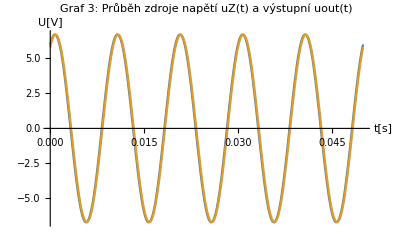

Pokud se vám zdá, že jsou grafy téměř totožné, zkuste zvýšit hodnotu rezistoru R2.

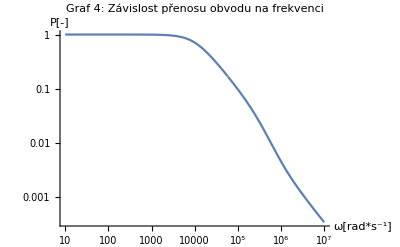

```mathematica
ClearAll["Global`*"]

(* Definice zdroje napětí *)
uZ = 3+6*ⅉ;
frekvence  = 100;
perioda = 1/frekvence;
tmax = 5*perioda;
tmax1 =0.3;

(* Převedu si zdroj napětí z fázoru do časové oblasti, abych se mohl podívat jak vypadá *)
φ = Arg[uZ];
amplituda= Abs[uZ];
omega = {ω->2*π*frekvence};
(* Definice funkce pro zdroj napětí v časové oblasti *)
uZ1[t_]:=amplituda*Sin[2*π*frekvence*t+φ]
uZ2[t_]:=amplituda*Im[ⅇ^(ⅉ*ω*t+ⅉ*φ)]/.omega

Plot[uZ1[t],{t,0,tmax}, AxesLabel->{"t[s]","U[V]"}, PlotLabel->"Graf 1: Průběh zdroje napětí uZ(t)"] (* tímto si ověřím, že zadefinovaný zdroj napětí, který jsem si převedl do časové oblasti je správný - že půjde vykreslit a bude mít požadovanou amplitudu, posun a frekvenci*)
Plot[uZ2[t],{t,0,tmax}, AxesLabel->{"t[s]","U[V]"}, PlotLabel->"Graf 2: Průběh zdroje napětí uZ(t) Graf 2 == Graf 1."](* tímto si ověřím další možný způsob převodu zadefinovaného zdroje napětí, který jsem si převedl do časové oblasti je správný - že půjde vykreslit a bude mít požadovanou amplitudu, posun a frekvenci, pod sebou bych měl vidět dva stejné grafy *)

soucastky={
R1-> 10*10^3,
R2->10*10^3,
R3->10*10^3,
L1->10*10^-3,
C2->10*10^-9
};


rovnice = {
iuZ==iL1+iR1, (* uzel u1 *)
iL1+iR1==iR2+iR3, (* uzel u2 *)
iR2==iC2, (* uzel u3 *)
(* rovnice pro zdroj a soucastky *)
uZ == u1, 
u1-u2==R1*iR1,
u2-u3==R2*iR2,
u2==R3*iR3,
u1-u2==ⅉ*ω*L1*iL1,
u3==1/(ⅉ*ω*C2)*iC2
};

nezname ={
iuZ,
iR1,iR2,iR3,
iC2,
iL1,
u1,u2,u3
};

(* řešení s omegou *)
(*reseni = Solve[rovnice/.soucastky/.omega, nezname]*)

(* řešení bez omegy *)
reseni = Solve[rovnice/.soucastky, nezname]

(* Určení přenosu P  - vyčíslení hodnoty přenosu *)
prenos = u3/u1/.reseni[[1]]; (* obecny tvar prenosu*)
Print["Obecný tvar přenosu ještě v komplexních číslech a s nevyčíslenou úhlovou frekvencí P = " , prenos ]

P = Abs[u3/u1/.reseni[[1]]/.omega]//N ; (* vycisleni *)
Print["Vyčíslení přenosu, pokud dosadíme frekvenci f = " ,frekvence, " Hz. Přenos je P = ", P ]

(* 
	Vykreselení grafu pro uout, kde uout je u3
*)
Plot[{uZ1[t],Im[(u3/.reseni[[1]])*ⅇ^(ⅉ*ω*t)/.omega]},{t,0,tmax}, AxesLabel->{"t[s]","U[V]"}, PlotLabel->"Graf 3: Průběh zdroje napětí uZ(t) a výstupní uout(t)"]
Print["Pokud se vám zdá, že jsou grafy téměř totožné, zkuste zvýšit hodnotu rezistoru R2."]
(*
	Vykreslení přenosu obovodu pro zadaný rozsah úhlové frekvence
*)
LogLogPlot[Abs[prenos],{ω,10,10^7},AxesLabel->{"ω[rad*s^-1]","P[-]"},PlotLabel->"Graf 4: Závislost přenosu obvodu na frekvenci"]
```